```mathematica
f[s0_,d0_,W0_]:=Module[{s=s0,Dif=d0,W=W0},
nt=1000;(*Teilnehmer*);n=2;(*MonteCarlo Läufe*)
W=Exp[-s^2/2+s#]&/@W;
EW=0;V=0;
For[i=1,i≤n,i++,
T=0;
For[j=1,j≤nt,j++,
If[W[[i,j]]-Dif/100>Total[W[[i]]]/nt,T++];
];
EW+=T;
V+=T^2;
];
EW/n/nt//N
]
```

```mathematica
W=RandomReal[NormalDistribution[],{n ,nt}];A=Table[f[a/10. Sqrt[1/12],b,W],{a,1,9},{b,0,15}];MatrixForm[A]
```

(0.499 | 0.3565 | 0.2435 | 0.155 | 0.0835 | 0.0445 | 0.02 | 0.009 | 0.002 | 0.0005 | 0. | 0. | 0. | 0. | 0. | 0.
0.4935 | 0.418 | 0.3515 | 0.292 | 0.2415 | 0.1995 | 0.155 | 0.1185 | 0.0855 | 0.068 | 0.0465 | 0.0335 | 0.0215 | 0.018 | 0.0105 | 0.007
0.4865 | 0.435 | 0.389 | 0.344 | 0.305 | 0.274 | 0.2385 | 0.2105 | 0.1795 | 0.155 | 0.132 | 0.1105 | 0.0875 | 0.0755 | 0.0605 | 0.0465
0.478 | 0.4435 | 0.4075 | 0.3715 | 0.341 | 0.3105 | 0.2875 | 0.2625 | 0.236 | 0.214 | 0.195 | 0.1695 | 0.155 | 0.137 | 0.119 | 0.1075
0.4745 | 0.4445 | 0.4155 | 0.388 | 0.3625 | 0.3375 | 0.3115 | 0.292 | 0.274 | 0.2515 | 0.2325 | 0.217 | 0.203 | 0.1835 | 0.1675 | 0.155
0.469 | 0.443 | 0.4185 | 0.3945 | 0.372 | 0.3525 | 0.3345 | 0.311 | 0.296 | 0.279 | 0.2655 | 0.2455 | 0.2315 | 0.2175 | 0.205 | 0.193
0.46 | 0.4395 | 0.4205 | 0.398 | 0.3775 | 0.3635 | 0.343 | 0.3305 | 0.31 | 0.298 | 0.283 | 0.272 | 0.2525 | 0.2425 | 0.2295 | 0.2175
0.453 | 0.4355 | 0.4185 | 0.4 | 0.382 | 0.3705 | 0.353 | 0.3375 | 0.324 | 0.3075 | 0.2975 | 0.2845 | 0.274 | 0.2625 | 0.248 | 0.2365
0.448 | 0.431 | 0.416 | 0.4 | 0.3855 | 0.371 | 0.3585 | 0.343 | 0.334 | 0.32 | 0.306 | 0.2955 | 0.285 | 0.2755 | 0.267 | 0.2515)

```mathematica
ListPlot3D[A,Mesh->All]
```

-Graphics3D-

```mathematica
f[4/10. Sqrt[3/12],10,W]
```

0.2765

```mathematica
10*1000*%
```

1705.

```mathematica
.5 0.9+.5 1.1
```

1.

```mathematica
500*30
```

15000

```mathematica
3 %
```

0.8295

```mathematica
1-%
```

0.1705

```mathematica
W
```

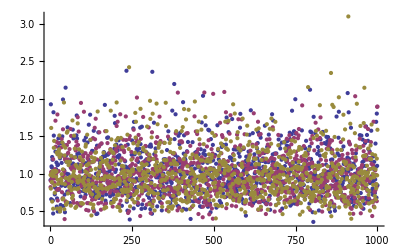

```mathematica
ListPlot[Transpose[W]]
```

```mathematica
Mean[#]&/@Transpose[W]
```

{1.0216,1.00833,0.996561}

```mathematica
Ew=13
```

13